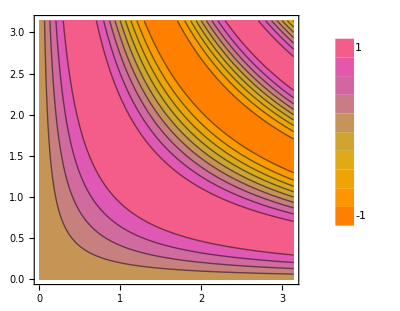

```mathematica
Needs["PlotLegends`"]
ShowLegend[ContourPlot[Sin[x y],{x,0,π},{y,0,π},Mesh->False,PlotPoints->30,ColorFunction->"FruitPunchColors"],{ColorData["FruitPunchColors"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-.6},LegendShadow->None,LegendSize->1.5}]
```

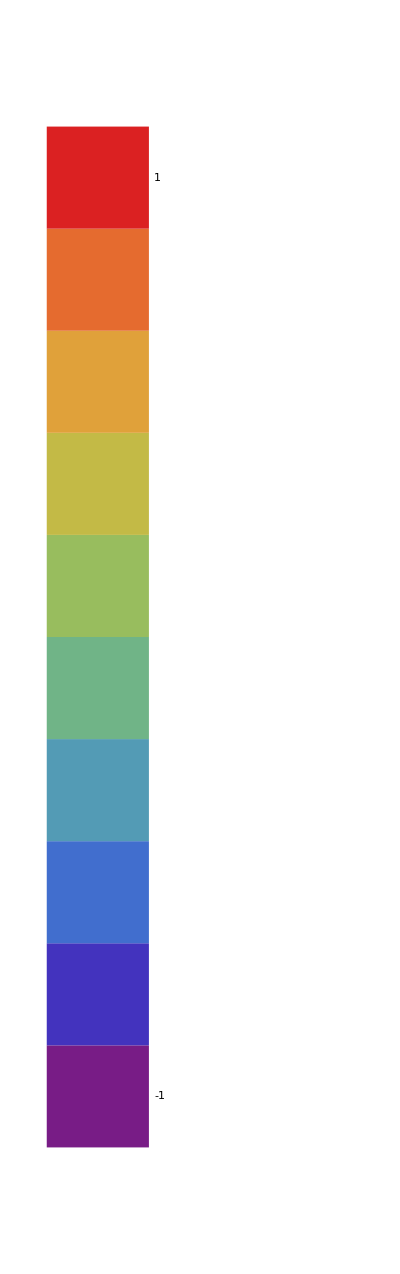

```mathematica
ShowLegend[Plot3D[Sin[x y],{x,0,π},{y,0,π},ColorFunction->"Rainbow"],{ColorData["Rainbow"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-.4}}]
```

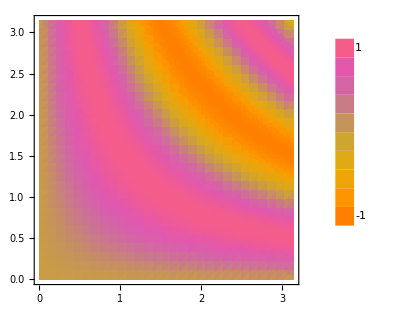

```mathematica
ShowLegend[DensityPlot[Sin[x y],{x,0,π},{y,0,π},Mesh->False,PlotPoints->30,ColorFunction->"FruitPunchColors"],{ColorData["FruitPunchColors"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-.6},LegendShadow->None,LegendSize->1.5}]
```

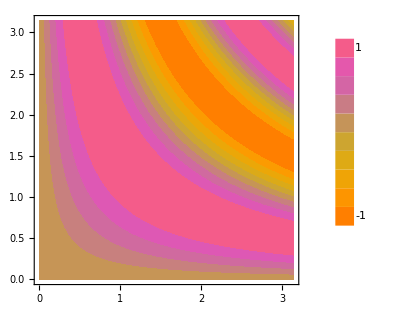

```mathematica
ShowLegend[ContourPlot[Sin[x y],{x,0,π},{y,0,π},Mesh->False,PlotPoints->30,ColorFunction->"FruitPunchColors",ContourStyle->None],{ColorData["FruitPunchColors"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-.6},LegendShadow->None,LegendSize->1.5}]
```